```mathematica
Clear[η1,η2,s]
```

```mathematica
(x+y)/2=w
(-x+y)/2=z

x=w-z
y=w+z
```

```mathematica
2 Q==1-x y +(η1-η2)√((1-x^2) (1-y^2))   /.{x-> w-z,y-> w+z} //FullSimplify
y==(1-sp)/(1+sp)x+(2s)/(1+sp)/.{x-> w-z,y-> w+z}//Simplify
```

2 Q+w^2+√((-1+w^2)^2-2 (1+w^2) z^2+z^4) (-η1+η2)==1+z^2

(-s+sp w+z)/(1+sp)==0

```mathematica
Solve[(-s+sp w+z)/(1+sp)==0,z]
```

{{z→s-sp w}}

```mathematica
((1-x^2) (1-y^2)/.{x-> w-z,y-> w+z} //ExpandAll)
```

1-2 w^2+w^4-2 z^2-2 w^2 z^2+z^4

```mathematica
(1+w^2-z^2)^2-4 w^2//ExpandAll
```

1-2 w^2+w^4-2 z^2-2 w^2 z^2+z^4

2 Q==1-(w^2-z^2) +(η1-η2)√((1+w^2-z^2)^2-4 w^2)   
z==-sp w+s

```mathematica
FullSimplify[Solve[2 Q==1-(w2-z2) +(η1-η2)√((1+w2-z2)^2-4w2),z2]//FullSimplify,0<η1<1/2<η2]
```

{{z2→(1-2 Q+w2 (-1+(η1-η2)^2)+(η1-η2) (η1+2 √(1+(-2+Q) Q+w2 (-1+(η1-η2)^2))-η2))/(-1+(η1-η2)^2)},{z2→(1-2 Q+w2 (-1+(η1-η2)^2)+(η1-η2) (η1-2 √(1+(-2+Q) Q+w2 (-1+(η1-η2)^2))-η2))/(-1+(η1-η2)^2)}}

```mathematica
(1-2 Q+w2 (-1+(η1-η2)^2)+(η1-η2) (η1±2 √(1+(-2+Q) Q+w2 (-1+(η1-η2)^2))-η2))/(-1+(η1-η2)^2)
```

```mathematica
FullSimplify[Solve[2 Q==1-(w2-z2) +(η1-η2)√((1+w2-z2)^2-4w2),z2]/. η2->1-η1//FullSimplify,0<η1<1/2<η2]
```

```mathematica
{{z2->(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2)},{z2->(-1+Q+2 (1+w2) η1 η2-(1-2 η1) √((1-Q)^2-4 w2 η1 η2))/(2  η1 η2)}}
```

```mathematica
((1-Q)/(2η1 η2))^2> w2
```

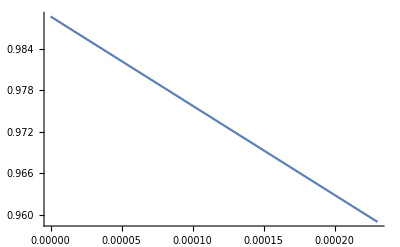

```mathematica
η1=.12;
η2=1-η1;
Q=.99;
Plot[(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2),{w2,0,1},PlotRange->{0,All}]
Clear[Q,η1,η2]
```

```mathematica
1+(-2+Q) Q-(1-Q)^2//Simplify
```

0

```mathematica
z'==0   -> ( √z2)'==  -> D[z2,w]/(2 √z2)==0 -> -> D[z2,w2]/(√z2)w==0  ->  D[z2,w2]==0
```

```mathematica
D[(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2),w2]//Simplify
```

(-1+2 η1+√(1-2 Q+Q^2-4 w2 η1 η2))/(√(1-2 Q+Q^2-4 w2 η1 η2))

```mathematica
Solve[-1+2 η1+√(1-2 Q+Q^2-4 w2 η1 η2)==0,w2]//FullSimplify
```

{{w2→((Q-2 η1) (-2+Q+2 η1))/(4 η1 η2)}}

```mathematica
w-> √(((Q-2 η1) (Q-2 η2))/(4 η1 η2))
```

```mathematica
(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2)/.w2-> ((Q-2 η1) (Q-2 η2))/(4 η1 η2)//FullSimplify
```

1/(4 η1 η2)(-2+Q^2+8 η1 η2-2 Q (-1+η1+η2)+2 √(1-4 η1 η2+2 Q (-1+η1+η2))-4 η1 √(1-4 η1 η2+2 Q (-1+η1+η2)))

```mathematica
1/(4 η1 η2)(-2+Q^2+8 η1 η2+2 (η2-η1)-4 η1 (η2-η1))//Simplify
```

```mathematica
Q^2/(4 η1 η2)
```

0.77

0.72

0.76

0.145834

{0.82717,0.943269}

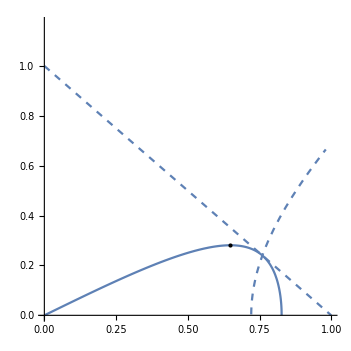

```mathematica
η1=.23; (*    η1≤ 1/4  *)
η2=1-η1
Q=η1; (* leftmost zero moves to $t=0$ and then disappears becoming a minimum *)
Q=2η1;(* minimum at t=0 disapears while maximum moves to t=0 *)
Q=1-2η1; (* rightmost zero vanishes. The slope becomes ∞ at t_max *)
Q=.9;

η1=.28;  (*   1/4 < η1≤ 1/3  *)
η2=1-η1
Q=η1; (* leftmost zero vanishes *)
Q=1-2η1; (* rightmost zero vanishes *)
Q=2η1;(* maximum moves to t=0 *)
Q=.9;

η1=.24;  (*   1/3 < η1 ≤ 1/2  *)
η2=1-η1
Q=1-2η1; (* rightmost zero vanishes *)
Q=η1; (* leftmost zero vanishes *)
Q=2η1;(* maximum moves to t=0 *)
Q=.24;

1-2 √(η1 η2)
{√((η2-Q)/η2),√((1-Q)/(2 √(η1 η2)))}

Show[Plot[√((-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2))/. w2-> w^2,{w,√Max[0,(η1-Q)/η1],√If[Q≤ 1-2η1,Min[(η2-Q)/η2,(1-Q)/(2 √(η1 η2))],(1-Q)/(2 √(η1 η2))]},PlotRange->{{0,1},{0,1/(2 √(η1 η2))}},AspectRatio-> 1],
Plot[√(-1+2 Q+w^2),{w,0,1-Q 1/(4 η1 η2)(-2+Q^2+8 η1 η2-2 Q (-1+η1+η2)+2 √(1-4 η1 η2+2 Q (-1+η1+η2))-4 η1 √(1-4 η1 η2+2 Q (-1+η1+η2)))},PlotStyle->Dashed],Plot[1-w,{w,0,1},PlotStyle->Dashed],Graphics[Point[If[Im[ç= √(((Q-2 η1) (Q-2 η2))/(4 η1 η2))]==0,{ç,Q/(2 √(η1 η2))},{0,√((Q-η1)/η2)}]]]]
Clear[η1,η2,Q]
```

```mathematica
Solve[√(-1+2 Q+w^2)==1-w,w]
```

{{w→1-Q}}

```mathematica
FullSimplify[(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2)/.w2->0//FullSimplify,{0<Q<1}]
```

(-1+Q+η2)/η2

```mathematica
(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2)/. {η1->1/2,η2->1/2}//FullSimplify
```

-1+2 Q+w2

```mathematica
Series[(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2)/. η2->1-η1,{η1,1/2,1}]
```

(-1+2 Q+w2)-4 √(1-2 Q+Q^2-w2) (η1-1/2)+O[η1-1/2]^2

0.77

0.72

0.86

0.306026

{0.806947,1.00433}

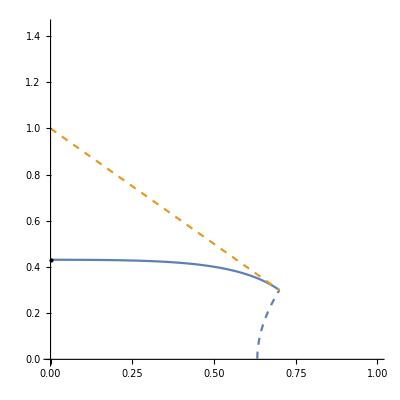

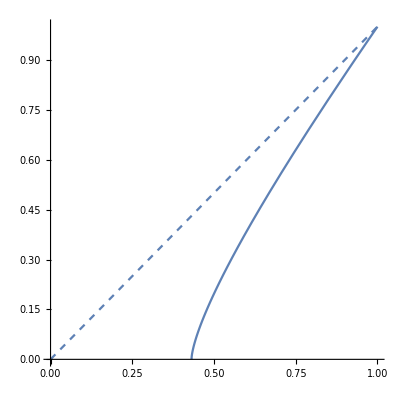

```mathematica
η1=.23; (*    η1≤ 1/4  *)
η2=1-η1
Q=η1; (* leftmost zero moves to $t=0$ and then disappears becoming a minimum *)
Q=2η1;(* minimum at t=0 disapears while maximum moves to t=0 *)
Q=1-2η1; (* rightmost zero vanishes. The slope becomes ∞ at t_max *)
Q=.9;

η1=.28;  (*   1/4 < η1≤ 1/3  *)
η2=1-η1
Q=η1; (* leftmost zero vanishes *)
Q=1-2η1; (* rightmost zero vanishes *)
Q=2η1;(* maximum moves to t=0 *)
Q=.9;

η1=.14;  (*   1/3 < η1 ≤ 1/2  *)
η2=1-η1
Q=1-2η1; (* rightmost zero vanishes *)
Q=η1; (* leftmost zero vanishes *)
Q=2η1;(* maximum moves to t=0 *)
Q=.3;

1-2 √(η1 η2)
{√((η2-Q)/η2),√((1-Q)/(2 √(η1 η2)))}

Show[Plot[√((-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2))/. w2-> w^2,{w,If[Q≤2η1,√(((Q-2 η1) (Q-2 η2))/(4 η1 η2)),0],1-Q},PlotRange->{{0,1},{0,1/(2 √(η1 η2))}},AspectRatio-> 1],
Plot[{√(-1+2 Q+w^2),1-w},{w,0,1-Q},PlotStyle->Dashed],Graphics[Point[If[Q≤ 2η1,{√(((Q-2 η1) (Q-2 η2))/(4 η1 η2)),Q/(2 √(η1 η2))},{0,√((Q-η1)/η2)}]]]]

Show[ParametricPlot[{thez-dz w,-dz},{w,If[Q≤2η1,√(((Q-2 η1) (Q-2 η2))/(4 η1 η2)),0],1-Q},AspectRatio-> 1,PlotRange->{{0,1},{0,1}}],Plot[x,{x,0,1},PlotStyle->Dashed]]
Clear[η1,η2,Q]
```

```mathematica
dz=D[thez=√((-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2))/. w2->w^2,w]
```

(4 w η1 η2-(4 w (1-2 η1) η1 η2)/(√((1-Q)^2-4 w^2 η1 η2)))/(2 √2 η1 η2 √((-1+Q+2 (1+w^2) η1 η2+(1-2 η1) √((1-Q)^2-4 w^2 η1 η2))/(η1 η2)))

0.9

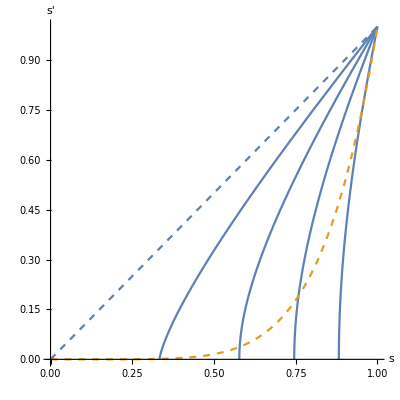

-Graphics3D-

```mathematica
η1=.1; (*    η1≤ 1/4  *)
η2=1-η1


Plo0=Show[Table[ParametricPlot[{thez-dz w,-dz},{w,If[Im[ç= √(((Q-2 η1) (Q-2 η2))/(4 η1 η2))]==0,ç,0],1-Q},AspectRatio-> 1,PlotRange->{{0,1},{0,1}}],{Q,.2,.8,.2}],Plot[{s,s^6},{s,0,1},PlotStyle->Dashed],AxesLabel->{Style[s,Medium ],Style[s',Medium]}]

Show[ParametricPlot3D[{thez-dz w,-dz,Q},{Q,10^-5,0.99},{w,If[Im[ç= √(((Q-2 η1) (Q-2 η2))/(4 η1 η2))]==0,ç,0],1-Q}],ParametricPlot3D[{s,s^6,Q},{Q,10^-5,0.99},{s,0,1}]]
Clear[η1,η2,Q]
```

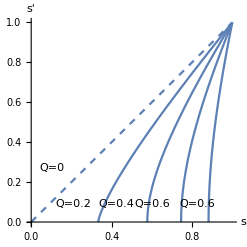

-Graphics3D-

{{0.,0.},{0.05,3.19176×10^-9},{0.1,6.23793×10^-11},{0.15,2.24565×10^-10},{0.2,0.},{0.25,1.24066×10^-10},{0.3,5.35647×10^-10},{0.35,0.0559079},{0.4,0.160843},{0.45,0.247809},{0.5,0.32736},{0.55,0.402467},{0.6,0.474558},{0.65,0.544433},{0.7,0.612603},{0.75,0.679415},{0.8,0.745118},{0.85,0.809899},{0.9,0.873902},{0.95,0.937238},{1.,1.}}

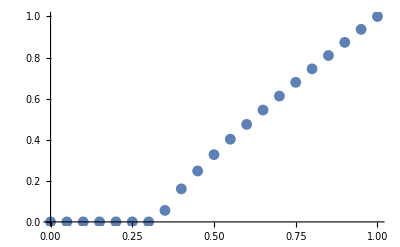

```mathematica
η1=.1; (*    η1≤ 1/4  *)
η2=1-η1;
s=.4;
Q=.2;
num1=Table[{s,(Minimize[{((s-Sin[θ1]Sin[θ2])/(Cos[θ1]Cos[θ2]))^2,Q==η1 Sin[θ1]^2+η2 Sin[θ2]^2,0≤ θ1≤ π/2,0≤ θ2≤ π/2},{θ1,θ2}][[1]])^(1/2)},{s,0,1,.05}]
Plo1=ListPlot[num1]

Clear[η1,η2,s,Q]
```

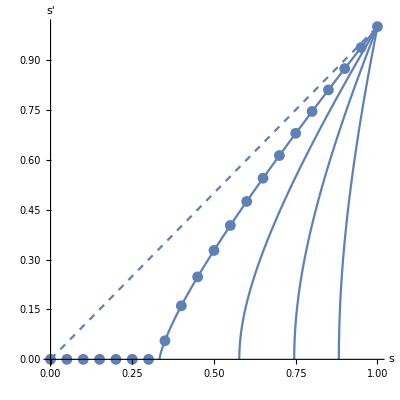

```mathematica
Show[Plo0,Plo1]
```

{{0.01,1.},{0.03,1.},{0.05,1.},{0.07,1.},{0.09,1.},{0.11,1.},{0.13,0.999946},{0.15,0.999744},{0.17,0.999413},{0.19,0.998973},{0.21,0.99844},{0.23,0.997833},{0.25,0.997166},{0.27,0.996455},{0.29,0.995716},{0.31,0.994953},{0.33,0.994185},{0.35,0.993421},{0.37,0.992669},{0.39,0.991941},{0.41,0.991238},{0.43,0.990574},{0.45,0.989954},{0.47,0.989379},{0.49,0.988859},{0.51,0.988397},{0.53,0.987998},{0.55,0.987663},{0.57,0.987399},{0.59,0.987201},{0.61,0.987078},{0.63,0.987029},{0.65,0.987057},{0.67,0.987164},{0.69,0.987343},{0.71,0.987603},{0.73,0.98795},{0.75,0.98836},{0.77,0.988854},{0.79,0.989427},{0.81,0.990079},{0.83,0.990807},{0.85,0.991613},{0.87,0.992494},{0.89,0.993449},{0.91,0.994479},{0.93,0.995582},{0.95,0.996757},{0.97,0.998002},{0.99,0.999317}}

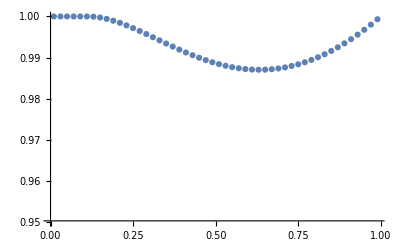

```mathematica
η1=.4; (*    η1≤ 1/4  *)
η2=1-η1;
Q=.1;
n=2;

num1=Table[{s,OU=NMinimize[{Abs[s^n-(s-Sin[θ1]Sin[θ2])/(Cos[θ1]Cos[θ2])],Q==η1 Sin[θ1]^2+η2 Sin[θ2]^2,s-Sin[θ1]Sin[θ2]≥0,0≤ θ1< π/2,0≤ θ2< π/2},{θ1,θ2}];1/2+1/(2(1-Q))√((1-Q)^2-4η1 η2  Cos[θ1]Cos[θ2] Sin[ArcCos[s^n]-ArcCos[(s-Sin[θ1]Sin[θ2])/(Cos[θ1]Cos[θ2])]]^2)/.OU[[2]]},{s,.01,.99,.02}]
Plo1=ListPlot[num1,PlotRange->{.95,1}]


Clear[η1,η2,s,Q]
```

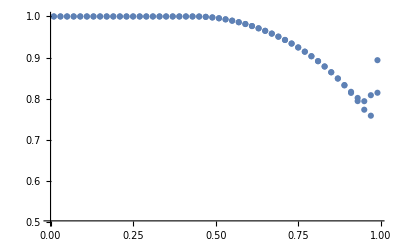

```mathematica
y100=Plo1;
Show[y50,y100]
```

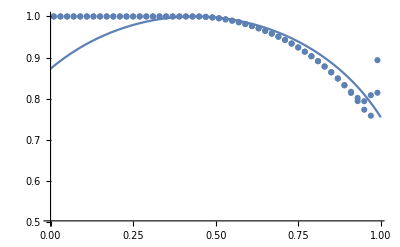

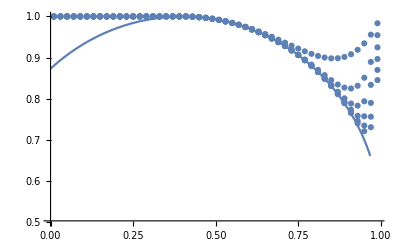

```mathematica
η1=.3; (*    η1≤ 1/4  *)
η2=1-η1;
Q=.4;
n=60;
pipom=Plot[1/(1-Q)1/2((1-Q)+√((1-Q)^2-(2 √(η1 η2)s-Q)^2)),{s,0,1}];
Show[y50,y100,pipom]
Clear[η1,η2,s,Q]
```

```mathematica
Clear[s,q1,q2]
η1=.45; (*    η1≤ 1/4  *)
η2=1-η1;
Q=.4;
s=.9;
Maximize[{η1 p1+η2 p2,η1 q1+η2 q2==Q,√(p1 (1-q2-p2))+√(p2 (1-q1-p1))+√(q1 q2)==s,0≤ p1≤ 1,0≤ p2≤ 1,0≤ q1≤ 1,0≤ q2≤ 1,0≤ p1+q1≤ 1,0≤ p2+q2≤ 1},{p1,p2,q1,q2}]
1/2((1-Q)+√((1-Q)^2-(2 √(η1 η2)s-Q)^2))
Clear[η1,η2,s,Q]
```

{0.469183,{p1→0.367247,p2→0.552584,q1→0.444444,q2→0.363637}}

0.469183

0.45

{{0.6,0.524528},{0.65,0.511803},{0.7,0.495214},{0.75,0.473953},{0.8,0.446665},{0.85,0.410814},{0.9,0.360713},{0.95,0.278087}}

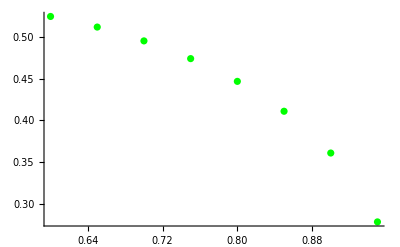

{{0.01,0.59},{0.03,0.59},{0.05,0.59},{0.07,0.59},{0.09,0.59},{0.11,0.59},{0.13,0.59},{0.15,0.59},{0.17,0.59},{0.19,0.59},{0.21,0.59},{0.23,0.59},{0.25,0.59},{0.27,0.59},{0.29,0.59},{0.31,0.59},{0.33,0.59},{0.35,0.59},{0.37,0.59},{0.39,0.59},{0.41,0.59},{0.43,0.589832},{0.45,0.589248},{0.47,0.588244},{0.49,0.586817},{0.51,0.584962},{0.53,0.58267},{0.55,0.579933},{0.57,0.576738},{0.59,0.573071},{0.61,0.568914},{0.63,0.564245},{0.65,0.55904},{0.67,0.553268},{0.69,0.546892},{0.71,0.539869},{0.73,0.532145},{0.75,0.523654},{0.77,0.514315},{0.79,0.504026},{0.81,0.492655},{0.83,0.480026},{0.85,0.465904},{0.87,0.449952},{0.89,0.431675},{0.91,0.4103},{0.93,0.38464},{0.95,0.353803},{0.97,0.32855},{0.99,0.410054}}

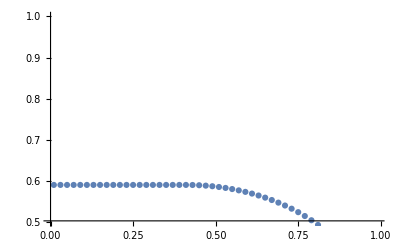

```mathematica
Clear[s,q1,q2]
η1=.45 (*    η1≤ 1/4  *)
η2=1-η1;
Q=.41;
n=100;
p1T=Table[{s,p1/.NMaximize[{1.(η1 p1+η2 p2),η1 q1+η2 q2==Q,√(p1 (1-q2-p2))+√(p2 (1-q1-p1))+√(q1 q2)==s,0≤ p1≤ 1,0≤ p2≤ 1,0≤ q1≤ 1,0≤ q2≤ 1,0≤ p1+q1≤ 1,0≤ p2+q2≤ 1},{p1,p2,q1,q2}][[2]]},{s,.6,.99,.05}]
p1P=ListPlot[p1T,PlotStyle->Green]
num1=Table[{s,OU=NMinimize[{Abs[s^n-(s-Sin[θ1]Sin[θ2])/(Cos[θ1]Cos[θ2])],Q==η1 Sin[θ1]^2+η2 Sin[θ2]^2,s-Sin[θ1]Sin[θ2]≥0,0≤ θ1< π/2,0≤ θ2< π/2},{θ1,θ2}];FF=1/2+1/2 √(1-4η1 η2 Sin[ArcCos[s^n]-ArcCos[(s-Sin[θ1]Sin[θ2])/(Cos[θ1]Cos[θ2])]]^2)/.OU[[2]];(1-Q)FF (1-(1-FF)/η1)/(2FF-1)},{s,.01,.99,.02}]
Plo1=ListPlot[num1,PlotRange->{.5,1}]

Clear[η1,η2,s,Q,n]
```

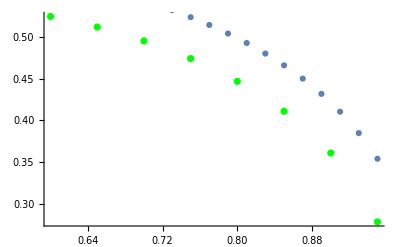

```mathematica
Show[p1P,Plo1]
```

```mathematica
s
```

0.26

```mathematica
η1=.4; (*    η1≤ 1/4  *)
η2=1-η1;
Q=0.1;
n=2;
thez=√((-1+Q+2 (1+t^2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 t^2))/(2η1 η2));


jaja=Table[{s,NMaximize[{(1-Q+√((1-Q)^2-4η1 η2(√(1-s^(2n))(s-thez)-√(t^2-(s-thez)^2)s^n)^2))/(2(1-Q)),If[Q≤2η1,√(((Q-2 η1) (Q-2 η2))/(4 η1 η2)),0]≤ t≤ 1-Q},t][[1]]},{s,.01,.9999,.01}];
pipom=Plot[1/(1-Q)1/2((1-Q)+√((1-Q)^2-(2 √(η1 η2)s-Q)^2)),{s,0,1},PlotStyle->Dotted,PlotRange->{.5,1}];




Clear[η1,η2,s,Q]
```

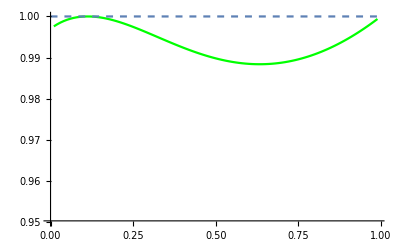

```mathematica
x2=ListPlot[jaja,Joined->True,PlotStyle->Green,PlotRange->{.95,1}];
Show[%,Plot[1,{x,0,1},PlotStyle->Dashed]]
```

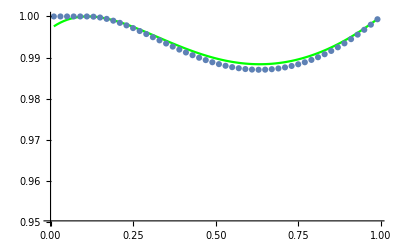

```mathematica
Show[x2,Plo1]
```

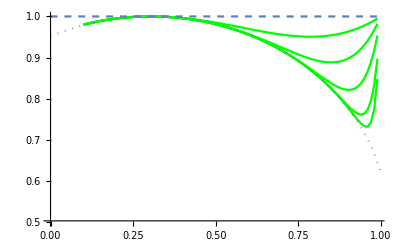

```mathematica
Show[x5,x10,x20,x40,x60,pipom,Plot[1,{x,0,1},PlotStyle->Dashed]]
```

```mathematica
η1=.4; (*    η1≤ 1/4  *)
η2=1-η1;
Q=0.3;
n=100;
s=.5;
thez=√((-1+Q+2 (1+t^2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 t^2))/(2η1 η2));


jeje=Table[{s,NMinimize[{(√(1-s^(2n))(s-thez)-√(t^2-(s-thez)^2)s^n)^2,If[Q≤2η1,√(((Q-2 η1) (Q-2 η2))/(4 η1 η2)),0]≤ t≤ 1-Q},t][[1]]},{s,.1,.9999,.01}]
(*pipom=Plot[1/(1-Q)1/2((1-Q)+√((1-Q)^2-(2 √(η1 η2)s-Q)^2)),{s,0,1},PlotStyle->Dotted,PlotRange->{.5,1}];*)




Clear[η1,η2,s,Q]
```

{{0.1,0.04},{0.11,0.0361},{0.12,0.0324},{0.13,0.0289},{0.14,0.0256},{0.15,0.0225},{0.16,0.0196},{0.17,0.0169},{0.18,0.0144},{0.19,0.0121},{0.2,0.01},{0.21,0.0081},{0.22,0.0064},{0.23,0.0049},{0.24,0.0036},{0.25,0.0025},{0.26,0.0016},{0.27,0.0009},{0.28,0.0004},{0.29,0.0001},{0.3,7.66017×10^-18},{0.31,0.0000145449},{0.32,0.000190821},{0.33,0.000567096},{0.34,0.00114337},{0.35,0.00191965},{0.36,0.00289592},{0.37,0.0040722},{0.38,0.00544847},{0.39,0.00702475},{0.4,0.00880103},{0.41,0.0107773},{0.42,0.0129536},{0.43,0.0153299},{0.44,0.0179061},{0.45,0.0206824},{0.46,0.0236587},{0.47,0.026835},{0.48,0.0302112},{0.49,0.0337875},{0.5,0.0375638},{0.51,0.0415401},{0.52,0.0457163},{0.53,0.0500926},{0.54,0.0546689},{0.55,0.0594452},{0.56,0.0644214},{0.57,0.0695977},{0.58,0.074974},{0.59,0.0805503},{0.6,0.0863265},{0.61,0.0923028},{0.62,0.0984791},{0.63,0.104855},{0.64,0.111432},{0.65,0.118208},{0.66,0.125184},{0.67,0.13236},{0.68,0.139737},{0.69,0.147313},{0.7,0.155089},{0.71,0.163066},{0.72,0.171242},{0.73,0.179618},{0.74,0.188194},{0.75,0.196971},{0.76,0.205947},{0.77,0.215123},{0.78,0.2245},{0.79,0.234076},{0.8,0.243852},{0.81,0.253828},{0.82,0.264005},{0.83,0.274381},{0.84,0.284957},{0.85,0.295733},{0.86,0.30671},{0.87,0.317886},{0.88,0.329261},{0.89,0.340835},{0.9,0.352604},{0.91,0.36456},{0.92,0.376678},{0.93,0.388895},{0.94,0.401044},{0.95,0.412703},{0.96,0.422829},{0.97,0.428654},{0.98,0.420861},{0.99,0.357305}}

0.77

0.72

0.76

0.145834

{0.82717,0.943269}

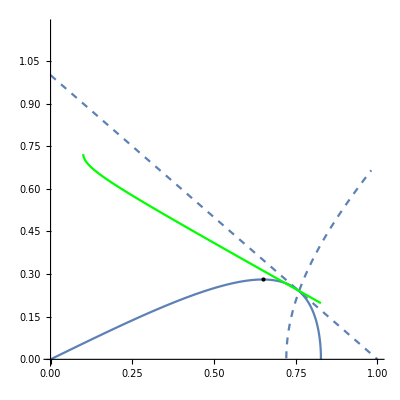

```mathematica
η1=.23; (*    η1≤ 1/4  *)
η2=1-η1
Q=η1; (* leftmost zero moves to $t=0$ and then disappears becoming a minimum *)
Q=2η1;(* minimum at t=0 disapears while maximum moves to t=0 *)
Q=1-2η1; (* rightmost zero vanishes. The slope becomes ∞ at t_max *)
Q=.9;

η1=.28;  (*   1/4 < η1≤ 1/3  *)
η2=1-η1
Q=η1; (* leftmost zero vanishes *)
Q=1-2η1; (* rightmost zero vanishes *)
Q=2η1;(* maximum moves to t=0 *)
Q=.9;

η1=.24;  (*   1/3 < η1 ≤ 1/2  *)
η2=1-η1
Q=1-2η1; (* rightmost zero vanishes *)
Q=η1; (* leftmost zero vanishes *)
Q=2η1;(* maximum moves to t=0 *)
Q=.24;

s=.8;
n=2;
Δ=.1;

1-2 √(η1 η2)
{√((η2-Q)/η2),√((1-Q)/(2 √(η1 η2)))}



Show[Plot[√((-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2))/. w2-> w^2,{w,√Max[0,(η1-Q)/η1],√If[Q≤ 1-2η1,Min[(η2-Q)/η2,(1-Q)/(2 √(η1 η2))],(1-Q)/(2 √(η1 η2))]},PlotRange->{{0,1},{0,1/(2 √(η1 η2))}},AspectRatio-> 1],
Plot[√(-1+2 Q+w^2),{w,0,1-Q 1/(4 η1 η2)(-2+Q^2+8 η1 η2-2 Q (-1+η1+η2)+2 √(1-4 η1 η2+2 Q (-1+η1+η2))-4 η1 √(1-4 η1 η2+2 Q (-1+η1+η2)))},PlotStyle->Dashed],Plot[1-w,{w,0,1},PlotStyle->Dashed],Graphics[Point[If[Im[ç= √(((Q-2 η1) (Q-2 η2))/(4 η1 η2))]==0,{ç,Q/(2 √(η1 η2))},{0,√((Q-η1)/η2)}]]],Plot[s-Δ √(1-s^(2n))-√(w^2-Δ^2)s^n,{w,√Max[0,(η1-Q)/η1],√If[Q≤ 1-2η1,Min[(η2-Q)/η2,(1-Q)/(2 √(η1 η2))],(1-Q)/(2 √(η1 η2))]},PlotStyle->Green]]
Clear[η1,η2,Q]
```

```mathematica
D[(-Qb+2 (1+w^2)  η1 η2+(1-2 η1) √(Qb^2-4η1 η2 w^2))/(2η1 η2),w]//FullSimplify
```

(2 w (-1+2 η1+√(Qb^2-4 w^2 η1 η2)))/(√(Qb^2-4 w^2 η1 η2))

```mathematica
Solve[(-Qb+2 (1+w2)  η1 η2+(1-2 η1) √(Qb^2-4η1 η2 w2))/(2η1 η2)==s-(2 w2 (-1+2 η1+√(Qb^2-4 w2 η1 η2)))/(√(Qb^2-4 w2  η1 η2)),Qb]
```

{{Qb→((-1+s-3 w2) η2)/(4 (-1+η1))-1/2 √(((-1+s-3 w2)^2 η2^2)/(4 (-1+η1)^2)+(2 η2 (3 w2-16 w2 η1+16 w2 η1^2+η1 η2-2 s η1 η2+s^2 η1 η2+6 w2 η1 η2-6 s w2 η1 η2+9 w2^2 η1 η2))/(3 (-1+η1))+(2^(1/3) (12 (-1+s-3 w2)^2 w2 η1 η2^3+η2^2 ((11)^2+48 w2 (-1+η1) η1 η2^2 (4 w2-16 w2 η1+16 w2 η1^2+η1 η2-2 s η1 η2+s^2 η1 η2+6 w2 η1 η2-6 s w2 η1 η2+9 w2^2 η1 η2)))/(3 (-1+η1) (7+√(-4 1+1))^(1/3))+((7+√(-4 (1)^3+(1)^2))^(1/3))/(3 2^(1/3) (-1+η1)))-1/2 √(((-1+s-3 w2)^2 η2^2)/(2 (-1+η1)^2)+(4 η2 (3 w2-16 w2 η1+16 w2 η1^2+η1 η2-2 s η1 η2+s^2 η1 η2+6 w2 η1 η2-6 s w2 η1 η2+9 w2^2 η1 η2))/(3 (-1+η1))-(2^(1/3) (12 (-1+s-3 w2)^2 w2 η1 η2^3+η2^2 (3 w2-16 w2 η1+16 w2 η1^2+η1 η2-2 s η1 η2+s^2 η1 η2+6 w2 η1 η2-6 s w2 η1 η2+9 w2^2 η1 η2)^2+48 w2 (-1+η1) η1 η2^2 (4 w2-16 w2 η1+16 w2 η1^2+η1 η2-2 s η1 η2+s^2 η1 η2+6 w2 η1 η2-6 s w2 η1 η2+9 w2^2 η1 η2)))/(3 (-1+η1) (7+√(-4 (12 (1)^2 w2 η1 η2^3+1+48 4 (1))^3+(1)^2))^(1/3))-((6+288 5 (1)+√(-4 (1)^3+(6+288 5 (1))^2))^(1/3))/(3 2^(1/3) (-1+η1))-(-(32 (-1+s-3 w2) w2 η1 η2^2)/(-1+η1)+((-1+s-3 w2)^3 η2^3)/(-1+η1)^3+(4 (-1+s-3 w2) η2^2 (3 w2-16 w2 η1+16 w2 η1^2+η1 η2-2 s η1 η2+s^2 η1 η2+6 w2 η1 η2-6 s w2 η1 η2+9 w2^2 η1 η2))/(-1+η1)^2)/(4 √(((-1+s-3 w2)^2 η2^2)/(4 (-1+η1)^2)+(2 η2 (3 w2-16 w2 η1+16 w2 η1^2+η1 η2-2 s η1 η2+s^2 η1 η2+6 w2 η1 η2-6 s w2 η1 η2+9 w2^2 η1 η2))/(3 (-1+η1))+(2^(1/3) (12 (-1+s-3 w2)^2 w2 η1 η2^3+η2^2 (3 w2-16 w2 η1+16 w2 η1^2+7+9 w2^2 η1 η2)^2+48 w2 (-1+η1) η1 η2^2 (4 w2-16 w2 η1+16 w2 η1^2+η1 η2-2 s η1 η2+s^2 η1 η2+6 w2 η1 η2-6 s w2 η1 η2+9 w2^2 η1 η2)))/(3 (-1+η1) (6+1+√(-4 (1)^3+(1)^2))^(1/3))+((6+1+√(-4 (12 (1)^2 w2 η1 η2^3+η2^2 1+1)^3+(1)^2))^(1/3))/(3 2^(1/3) (-1+η1)))))},{Qb→1},1,{Qb→((-1+s-3 w2) η2)/(4 (-1+η1))+1/2 √1+1/2 √(((1)^2 η2^2)/(2 (1)^2)+(4 η2 (1))/(3 (1))-1-1/1+1/(4 √1))}}
 |  |  |  |

```mathematica
-((-1+A-w2) +(1-2 η1) √(-4 w2+(1-A+w2)^2))/2//FullSimplify
```

1/2 (1-A+w2+√(-4 w2+(1-A+w2)^2) (-1+2 η1))

```mathematica
-4 w2+(1-A+w2)^2//Factor
```

1-2 A+A^2-2 w2-2 A w2+w2^2

```mathematica
Solve[(2t(1-2η1-√(Qb^2-4η1 η2 t^2)))/(√(Qb^2-4η1 η2 t^2))==B,Qb]//FullSimplify
```

{{Qb→-(2 t √((1-2 η1)^2+(B+2 t)^2 η1 η2))/(√((B+2 t)^2))},{Qb→(2 t √((1-2 η1)^2+(B+2 t)^2 η1 η2))/(√((B+2 t)^2))}}

```mathematica
Solve[(2 t √((1-2 η1)^2+((t s^n)/(√(t^2-Δ^2))+2 t)^2 η1 η2))/((t s^n)/(√(t^2-Δ^2))+2 t)==1/2 (1-(s-Δ √(1-s^(2n))-√(t^2-Δ^2)s^n)^2+t^2+√(-4 t^2+(1-(s-Δ √(1-s^(2n))-√(t^2-Δ^2)s^n)^2+t^2)^2) (-1+2 η1)),Δ]
```

$Aborted

```mathematica
(√((1-2 η1)^2+((t s^n)/(√(t^2-Δ^2))+2 t)^2 η1 η2))/(s^n/(√(t^2-Δ^2))+2)==1/4 (1-(s-Δ √(1-s^(2n))-√(t^2-Δ^2)s^n)^2+t^2+√(-4 t^2+(1-(s-Δ √(1-s^(2n))-√(t^2-Δ^2)s^n)^2+t^2)^2) (-1+2 η1))
```

### Other

0.77

0.158335

{0.+0.410891 ⅈ,0.344691}

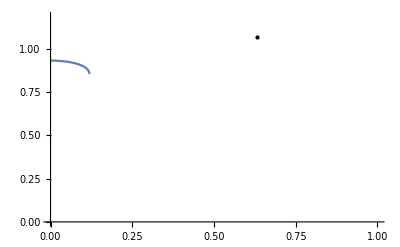

```mathematica
η1=.23;
η2=1-η1
Q=.9;
1-2 √(η1 η2)
{√((η2-Q)/η2),√((1-Q)/(2 √(η1 η2)))}

Show[Plot[√((-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2))/. w2-> w^2,{w,0,(1-Q)/(2 √(η1 η2))},PlotRange->{{0,1},{0,1/(2 √(η1 η2))}}],Graphics[Point[{Abs[ √(((Q-2 η1) (Q-2 η2))/(4 η1 η2))],Q/(2 √(η1 η2))}]]]
Clear[η1,η2,Q]
```

```mathematica
Solve[(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2)==0,w2]//FullSimplify
```

{{w2→(-Q+√(Q^2+4 η1 (-1+η1+η2))-2 η1 (-2+2 η1+η2+√(Q^2+4 η1 (-1+η1+η2))))/(2 η1 η2)},{w2→1/2 (-2-(Q+√(Q^2+4 η1 (-1+η1+η2))-2 η1 (2-2 η1+√(Q^2+4 η1 (-1+η1+η2))))/(η1 η2))}}

```mathematica
{{w2->(-Q+Q-2 η1 (-2+2 η1+η2+Q))/(2 η1 η2)},{w2->1/2 (-2-(Q+Q-2 η1 (2-2 η1+Q))/(η1 η2))}}//Simplify
```

{{w2→-(-2+Q+2 η1+η2)/η2},{w2→(Q (-1+η1)-η1 (-2+2 η1+η2))/(η1 η2)}}

```mathematica
-1-(Q- η1 (2-2 η1+Q))/(η1 η2)/. η2->1-η1//Simplify
```

1-Q/η1

z=√((-1+Q+2 (1+w^2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w^2))/(2η1 η2))   
z==-sp w+s

```mathematica
D[(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2),w2]/(√((-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2)))w//Simplify
```

(√2 w (-1+2 η1+√(1-2 Q+Q^2-4 w2 η1 η2)))/(√(1-2 Q+Q^2-4 w2 η1 η2) √((-1+Q+2 (1+w2) η1 η2+(1-2 η1) √(1-2 Q+Q^2-4 w2 η1 η2))/(η1 η2)))

```mathematica
2η1 η2(-sp w+s)^2+1-Q-2 (1+w^2)  η1 η2==(1-2 η1) √((1-Q)^2-4η1 η2 w^2)
(2η1 η2(-sp w+s)^2+1-Q-2 (1+w^2)  η1 η2)^2==(1-2 η1)^2 ((1-Q)^2-4η1 η2 w^2)
```

```mathematica
x^4+a x^3+b x^2+c x+d==0
(x-A)^2(x^2+B x+C)
```

```mathematica
(x-A)^2(x^2+B x+C)==x^4+a x^3+b x^2+c x+d//Expand
```

A^2 C+A^2 B x-2 A C x+A^2 x^2-2 A B x^2+C x^2-2 A x^3+B x^3+x^4==d+c x+b x^2+a x^3+x^4

```mathematica
A^2 C+A^2 B x-2 A C x+A^2 x^2-2 A B x^2+C x^2-2 A x^3+B x^3==d+c x+b x^2+a x^3
```

```mathematica
B-2A==a
A^2-2AB+C==b
A^2 B-2 A C==c
A^2 C==d
```

```mathematica
Solve[{BB-2AA==a,
AA^2-2AA BB+CC==b,
AA^2 BB-2 AA CC==c,
AA^2 CC==d},{AA,BB,CC}]
```

{}

```mathematica
B==a+2A
A^2-2A(a+2A)+C==b
A^2(a+2A)-2 A C==c
A^2 C==d
```

```mathematica
-3 A^2-2A a+C==b
2 A^3+a A^2-2 A C==c
A^2 C==d
```

```mathematica
-3 A^4-2 A^3 a+d==b A^2
2 A^4+a A^3-2 d==c A
A^2 C==d
```

```mathematica
-6 A^4-4a A^3+2d==2b A^2
6 A^4+3a A^3-6 d==3c A
```

```mathematica
a A^3+2b A^2+3c A+4d==0
```

```mathematica
-6 A^4-4 A^3 a+2d==2b A^2
2 A^4+a A^3-2 d==c A
```

```mathematica
4 A^3+3a A^2+2b A+c==0
```

```mathematica
4a A^3+8b A^2+12c A+16d==0
-4a A^3-3 a^2 A^2-2a b A-a c==0

(****************************)

-a c A^3-2b c A^2-3 c^2 A-4c d==0
16 d A^3+12a d A^2+8b d A+4c d==0
```

```mathematica
(8b-3 a^2)A^2+2(6c-a b)A+(16 d-a c)==0
(16 d-a c)A^2+2(6a d-b c)A+(8 b d-3 c^2)==0
```

```mathematica
(16d-a c)(8b-3 a^2)A^2+2(16d-a c)(6c-a b)A+(16 d-a c)^2==0
-(16d-a c)(8b-3 a^2)A^2-2(6a d-b c)(8b-3 a^2)A-(8 b d-3 c^2)(8b-3 a^2)==0

(********************************)

-(8b-3 a^2)(8 b d-3 c^2)A^2-2(8 b d-3 c^2)(6c-a b)A-(8 b d-3 c^2)(16 d-a c)==0
(16 d-a c)^2 A^2+2(6a d-b c)(16 d-a c)A+(8 b d-3 c^2)(16 d-a c)==0
```

```mathematica
(2(16d-a c)(6c-a b)-2(6a d-b c)(8b-3 a^2))A+(16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2)==0
((16 d-a c)^2-(8b-3 a^2)(8 b d-3 c^2))A+(2(6a d-b c)(16 d-a c)-2(8 b d-3 c^2)(6c-a b))==0
```

```mathematica
A-> 1/2((16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2))/((6a d-b c)(8b-3 a^2)-(16d-a c)(6c-a b))

A->2 ((8 b d-3 c^2)(6c-a b)-(6a d-b c)(16 d-a c))/((16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2))
```

A→((-a c+16 d)^2-(-3 a^2+8 b) (-3 c^2+8 b d))/(-6 (-3 a b+2 c) (-a c+16 d)+2 (-3 a^2+8 b) (-b c+6 a d))

```mathematica
(x-2)^2(x^2+ x+1)//ExpandAll
```

4+x^2-3 x^3+x^4

```mathematica
(2(8 b d-3 c^2)(6c-a b)-2(6a d-b c)(16 d-a c))/((16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2))/. {a-> -3,b-> 1,c-> 0,d->4}
```

2

```mathematica
Solve[{BB-2AA==-3,
AA^2-2AA BB+CC==1,
AA^2 BB-2 AA CC==0,
AA^2 CC==4},{AA,BB,CC}]
```

{{AA→2,BB→1,CC→1}}

```mathematica
((16 d-a c)^2-(8b-3 a^2)(8 b d-3 c^2))A+(2(6a d-b c)(16 d-a c)-2(8 b d-3 c^2)(6c-a b))/. {A-> 2,a-> -3,b-> 1,c-> 0,d->4}
```

0

```mathematica
A-> 1/2((16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2))/((6a d-b c)(8b-3 a^2)-(16d-a c)(6c-a b))

A->2 ((8 b d-3 c^2)(6c-a b)-(6a d-b c)(16 d-a c))/((16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2))
```

```mathematica
({{16 d-a c, 8 b d-3 c^2}, {8b-3 a^2, 16 d-a c}})
({{□, □}, {□, □}})
```

```mathematica
(4 (((8 b d-3 c^2)(6c-a b)-(6a d-b c)(16 d-a c))((6a d-b c)(8b-3 a^2)-(16d-a c)(6c-a b)))/(((16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2))^2)//ExpandAll)//FullSimplify
```

-((-c ((a^2-4 b) b+3 a c)+(9 a^3-32 a b+48 c) d) (-9 c^3+3 a^2 c d+32 b c d+a (b c^2-4 b^2 d-48 d^2)))/(4 (-3 b c^2+8 b^2 d+4 a c d-32 d^2+a^2 (c^2-3 b d))^2)

```mathematica
4 (((8 b d-3 c^2)(6c-a b)-(6a d-b c)(16 d-a c))((6a d-b c)(8b-3 a^2)-(16d-a c)(6c-a b)))/(((16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2))^2)/. {a-> -3,b-> 1,c-> 0,d->4}
```

1

```mathematica
((16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2))^2-4((8 b d-3 c^2)(6c-a b)-(6a d-b c)(16 d-a c))((6a d-b c)(8b-3 a^2)-(16d-a c)(6c-a b))/. {a-> -3,b-> 1,c-> 0,d->4}
```

0

```mathematica
Disc[a_,b_,c_,d_]:=((16 d-a c)^2-(8 b d-3 c^2)(8b-3 a^2))^2-4((8 b d-3 c^2)(6c-a b)-(6a d-b c)(16 d-a c))((6a d-b c)(8b-3 a^2)-(16d-a c)(6c-a b))
```

```mathematica
Disc[-3,1,0,4]
```

0

```mathematica
PP=(2η1 η2(-sp w+s)^2+1-Q-2 (1+w^2)  η1 η2)^2-(1-2 η1)^2 ((1-Q)^2-4η1 η2 w^2)
```

-(1-2 η1)^2 ((1-Q)^2-4 w^2 η1 η2)+(1-Q+2 (s-sp w)^2 η1 η2-2 (1+w^2) η1 η2)^2

```mathematica
sb1=1/(4!)D[PP,{w,4}]/. w->0//FullSimplify
aa=1/(3!)D[PP,{w,3}]/. w->0//FullSimplify
bb=1/(2!)D[PP,{w,2}]/. w->0//FullSimplify
cc=1/(1!)D[PP,{w,1}]/. w->0//FullSimplify
dd=PP/. w->0/FullSimplify
```

4 (-1+sp^2)^2 η1^2 η2^2

-16 s sp (-1+sp^2) η1^2 η2^2

4 η1 η2 (Q-Q sp^2+2 η1 (-2+2 η1+η2-s^2 η2)+sp^2 (1-2 η1 η2+6 s^2 η1 η2))

8 s sp η1 η2 (-1+Q-2 (-1+s^2) η1 η2)

-(1-Q)^2 (1-2 η1)^2+(1-Q-2 η1 η2+2 s^2 η1 η2)^2

```mathematica
4 η1 η2 (Q-Q sp^2+2 η1 (-η2-s^2 η2)+sp^2 (1-2 η1 η2+6 s^2 η1 η2))//Simplify
```

4 η1 η2 (Q-Q sp^2-2 (1+s^2) η1 η2+sp^2 (1-2 η1 η2+6 s^2 η1 η2))

```mathematica
1/(2!)D[PP,{w,1}]/. w->0//FullSimplify
```

4 s sp η1 η2 (-1+Q-2 (-1+s^2) η1 η2)

```mathematica
4 (1-sp^2)^2 η1^2 η2^2
```

```mathematica
aaa=aa/sb1//FullSimplify
bbb=bb/sb1//FullSimplify
ccc=cc/sb1//FullSimplify
ddd=dd/sb1//FullSimplify
```

-(4 s sp)/(-1+sp^2)

(Q-Q sp^2+2 η1 (-2+2 η1+η2-s^2 η2)+sp^2 (1-2 η1 η2+6 s^2 η1 η2))/((-1+sp^2)^2 η1 η2)

(2 s sp (-1+Q-2 (-1+s^2) η1 η2))/((-1+sp^2)^2 η1 η2)

-((-1+Q+η2-s^2 η2) ((-1+Q) (-1+η1)+(-1+s^2) η1 η2))/((-1+sp^2)^2 η1 η2^2)

```mathematica
af=(4 s sp)/(1-sp^2)
bf=(Q-Q sp^2-2 η1η2 (1+s^2)+sp^2 (1-2 η1 η2+6 s^2 η1 η2))/((1-sp^2)^2 η1 η2)

cf=2 s sp(2 (1-s^2) η1 η2-(1-Q))/((1-sp^2)^2 η1 η2)
df=((Q-η1-s^2 η2) (Q-η2-s^2 η1 ))/((1-sp^2)^2 η1 η2)
```

```mathematica
-2 s^2 η1 η2-1+2η1 η2+Q
```

```mathematica
-(η1-η2)^2-2η1 η2-1+4
```

```mathematica
bbb/. η2->1-η1//FullSimplify
```

(Q (-1+sp^2)-2 (1+s^2) (-1+η1) η1+sp^2 (-1+2 (-1+3 s^2) (-1+η1) η1))/((-1+sp^2)^2 (-1+η1) η1)

```mathematica
HHH=(-1+sp^2)^13 (-1+η1)^8 η1^6 Disc[aaa,bbb,ccc,ddd]/. η2->1-η1 //Simplify
```

1024 ((-1+sp^2) (-2 (-1+η1)^2 η1 (2 Q^2 (-1+sp^2)+Q (2-2 sp^2-s^2 (-2+sp^2))+2 s^4 (-1+η1) η1-2 (-1+sp^2) (-1+η1) η1+s^2 (-2+sp^2) (1-2 η1+2 η1^2))^2+(Q-Q sp^2+2 (1+s^2) (-1+η1) η1+sp^2 (1-2 η1+2 η1^2)) (-3 s^2 sp^2 (1-η1) (-1+Q+2 (-1+s^2) (-1+η1) η1)^2-2 (Q+s^2 (-1+η1)-η1) (-1+η1) (-1+Q+η1-s^2 η1) (Q-Q sp^2+2 (1+s^2) (-1+η1) η1+sp^2 (1+2 (-1+η1) η1-6 s^2 (-1+η1) η1))))^2-s^2 sp^2 (1-2 η1)^4 (-1+η1)^2 (-Q^3 (-1+sp^2)^2+sp^4 (1-2 η1+2 η1^2)+Q^2 (-1+sp^2) (-1-2 (7+s^2) η1+2 (7+s^2) η1^2+sp^2 (3-2 η1+2 η1^2))+2 sp^2 (-1+η1) η1 (2+4 η1-4 η1^2+s^2 (3-4 η1+4 η1^2))+Q (4 (4+3 s^2) (-1+η1) η1+sp^4 (-3+4 η1-4 η1^2)+sp^2 (2+8 (2+s^2) η1-8 (2+s^2) η1^2))+4 η1 (4 (-1+η1)^2 η1+2 s^4 (-1+η1)^2 η1+s^2 (3-9 η1+12 η1^2-6 η1^3))) (-6 Q^4 (-1+sp^2)^2-Q^3 (-1+sp^2) (14-18 sp^2+s^2 (6+sp^2))+8 s^6 (-1+η1)^2 η1^2+2 s^4 (-1+η1) η1 (-4 (1-2 η1)^2+sp^2 (3-4 η1+4 η1^2))+2 η1 (3 sp^4 (-1+η1)-8 (-1+η1)^2 η1+4 sp^2 (1-2 η1^2+η1^3))+s^2 (sp^4 (1-2 η1+2 η1^2)+8 η1 (-2+7 η1-10 η1^2+5 η1^3)+sp^2 (-1+14 η1-30 η1^2+32 η1^3-16 η1^4))+Q^2 (-8-22 η1+2 s^4 (3+sp^2) (-1+η1) η1+22 η1^2+6 sp^4 (-3-η1+η1^2)-4 sp^2 (-7-5 η1+5 η1^2)+s^2 (-14+20 η1-20 η1^2+sp^4 (3-2 η1+2 η1^2)+sp^2 (9-2 η1+2 η1^2)))+Q (-24 (-1+η1) η1-8 s^4 sp^2 (-1+η1) η1+sp^4 (6+12 η1-12 η1^2)+4 sp^2 (-2-7 η1+7 η1^2)+s^2 (sp^4 (-3+4 η1-4 η1^2)+8 (1-η1+η1^2)+3 sp^2 (-1-4 η1+4 η1^2)))))

```mathematica
D[HHH,{Q,7}]/. Q->0//FullSimplify
```

-10321920 (-1+sp^2)^4 (-4+12 sp^2+s^2 (-4+sp^2)) (1-2 η1)^4 (-1+η1)^2

{{0.377964},{0.+1. ⅈ}}

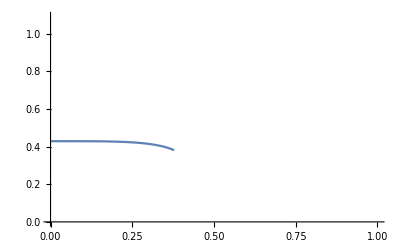

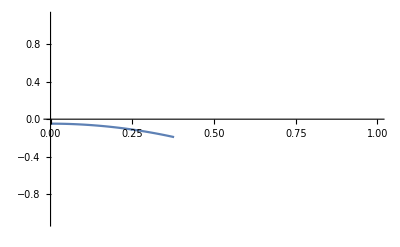

{0.142857,0.436436}

```mathematica
η1=.3;
η2=1-η1;
Q=.6;
{{√((η2-Q)/η2)},{√(-1-(Q- η1 (2-2 η1+Q))/(η1 η2))}}

Plot[(-1+Q+2 (1+w2)  η1 η2+(1-2 η1) √((1-Q)^2-4η1 η2 w2))/(2η1 η2)/. w2-> w^2,{w,√Max[0,(η1-Q)/η1],√Min[(η2-Q)/η2,(1-Q)/(2 √(η1 η2))]},PlotRange->{{0,1},{0,1/(2 √(η1 η2))}}]
Plot[-(-1+Q+2 (1+w2)  η1 η2)/(2η1 η2)/. w2-> w^2,{w,√Max[0,(η1-Q)/η1],√Min[(η2-Q)/η2,(1-Q)/(2 √(η1 η2))]},PlotRange->{{0,1},{-1/(2 √(η1 η2)),1/(2 √(η1 η2))}}]
{(η2-Q)/η2,(1-Q)/(2 √(η1 η2))}
Clear[η1,η2,Q]
```

```mathematica
√(1-4η1 η2)√((1-Q)^2-4η1 η2 w2)>1-Q-2 (1+w2)  η1 η2
```

```mathematica
(1-4η1 η2)((1-Q)^2-4η1 η2 w2 )>(1-Q-2 (1+w2)  η1 η2)^2
(1-Q)^2-4η1 η2 w2-4η1 η2((1-Q)^2-4η1 η2 w2 )>(1-Q)^2-4 (1+w2)  η1 η2(1-Q)+4 (1+w2)^2  η1^2 η2^2
- w2-(1-Q)^2+4η1 η2 w2 >-(1+w2) (1-Q)+ (1+w2)^2  η1 η2
Q-Q^2+4η1 η2 w2 >Q w2+ (1+w2)^2  η1 η2
```

```mathematica
4>(1+w2)^2
```

```mathematica
1-Q> w2
```

```mathematica
(1-4η1 η2)((1-Q)^2-4η1 η2 w2 )>(1-Q-2 (1+w2)  η1 η2)^2//FullSimplify
```

```mathematica
FullSimplify[η1 η2 (Q (-1+Q+w2)+(-1+w2)^2 η1 η2)<0,{0<η1<1,0<η2<1,0<Q<1,0<w2<1,(-1+Q)^2>4 w2 η1 η2}]
```

Q (-1+Q+w2)+(-1+w2)^2 η1 η2<0

```mathematica
FullSimplify[(1-Q)^2-4η1 η2 w2>0,{0<η1<1,0<η2<1,0<Q<1,0<w2<1}]
```

(-1+Q)^2>4 w2 η1 η2

```mathematica
(1-w2)^2 η1 η2<Q (1-Q-w2)
```

```mathematica
(1-Q)/(2 √(η1 η2))>1-Q
```

```mathematica
Q-Q^2+4η1 η2 w2 >Q w2+ (1+w2)^2  η1 η2
```

```mathematica
Q(1-Q)^2/(4η1 η2)+ (1+(1-Q)^2/(4η1 η2))^2  η1 η2//FullSimplify
```

1/2 (-1+Q)^2+((-1+Q^2)^2)/(16 η1 η2)+η1 η2

```mathematica
Solve[(2(1  -(1-2 η1)/(√((1-Q)^2-4 w2 η1 η2)))^2)/((-1+Q+2 (1+w2) η1 η2+(1-2 η1) √((1-Q)^2-4 w2 η1 η2))/(η1 η2))==sp^2/w2,w2]
```

$Aborted

```mathematica
(2(1  -(1-2 η1)/(√((1-Q)^2-4 w2 η1 η2)))^2)/((-1+Q+2 (1+w2) η1 η2+(1-2 η1) √((1-Q)^2-4 w2 η1 η2))/(η1 η2))==sp^2/w2
```

```mathematica
^□
```

```mathematica
Solve[(1-Q)^2-4 w2 η1 η2==x^2,w2]
```

{{w2→(1-2 Q+Q^2-x^2)/(4 η1 η2)}}

```mathematica
Solve[(2(1  -(1-2 η1)/x)^2)/((-1+Q+2 (1+(1-2 Q+Q^2-x^2)/(4 η1 η2)) η1 η2+(1-2 η1) x)/(η1 η2))==sp^2/((1-2 Q+Q^2-x^2)/(4 η1 η2)),x]
```

{{x→1/2 (1-2 η1)-1/2 √1-1/2 √(2 (-1+2 η1)^2-(-2 Q+Q^2+sp^2-Q^2 sp^2+4 η1-4 η1^2-4 sp^2 η1 η2)/(-1+sp^2)+(2 Q-Q^2-sp^2+Q^2 1-4 η1+4 η1^2+4 sp^2 η1 η2)/(3 (-1+sp^2))-1/(6 2 1)-(1+5+√1)^(1/3)/(12 2^(1/3) (-1+sp^2))-(-8 (-1+2 η1)^3-(16 (-1+2 Q-Q^2+2 η1-4 Q η1+2 Q^2 η1))/(-1+sp^2)+(8 (-1+2 η1) (-2 Q+Q^2+sp^2-Q^2 sp^2+4 η1-4 η1^2-4 sp^2 η1 η2))/(-1+sp^2))/(4 √((-1+2 η1)^2-(-2 Q+Q^2+sp^2-Q^2 sp^2+4 η1-4 η1^2-4 sp^2 η1 η2)/(-1+sp^2)-(8+4 η1^2+4 sp^2 η1 η2)/(3 (-1+sp^2))+1/(6 2^(2/3) (-1+sp^2) (1)^(1/3))+(1)^(1/3)/(12 2^(1/3) (-1+sp^2)))))},{x→1},{1},{x→1}}
 |  |  |  |

```mathematica
PPPP=(2η1 η2 x^2)/(-1+sp^2)(((1-2 Q+Q^2-x^2) (1-(1-2 η1)/x)^2)/(2 η1 η2)-(sp^2 (-1+Q+x (1-2 η1)+2 η1 (1+(1-2 Q+Q^2-x^2)/(4 η1 η2)) η2))/(η1 η2))/.x->x-(-2+4 η1)/4//ExpandAll
```

3/(16 (-1+sp^2))-Q/(2 (-1+sp^2))+Q^2/(4 (-1+sp^2))+sp^2/(16 (-1+sp^2))-(Q^2 sp^2)/(4 (-1+sp^2))+x/(2 (-1+sp^2))-(2 Q x)/(-1+sp^2)+(Q^2 x)/(-1+sp^2)-(Q^2 sp^2 x)/(-1+sp^2)-x^2/(2 (-1+sp^2))-(2 Q x^2)/(-1+sp^2)+(Q^2 x^2)/(-1+sp^2)-(sp^2 x^2)/(2 (-1+sp^2))-(Q^2 sp^2 x^2)/(-1+sp^2)-(2 x^3)/(-1+sp^2)-x^4/(-1+sp^2)+(sp^2 x^4)/(-1+sp^2)+3/(16 (-1+sp^2) (1/2+x-η1)^2)-Q/(2 (-1+sp^2) (1/2+x-η1)^2)+Q^2/(4 (-1+sp^2) (1/2+x-η1)^2)+x/(2 (-1+sp^2) (1/2+x-η1)^2)-(2 Q x)/((-1+sp^2) (1/2+x-η1)^2)+(Q^2 x)/((-1+sp^2) (1/2+x-η1)^2)-x^2/(2 (-1+sp^2) (1/2+x-η1)^2)-(2 Q x^2)/((-1+sp^2) (1/2+x-η1)^2)+(Q^2 x^2)/((-1+sp^2) (1/2+x-η1)^2)-(2 x^3)/((-1+sp^2) (1/2+x-η1)^2)-x^4/((-1+sp^2) (1/2+x-η1)^2)-3/(8 (-1+sp^2) (1/2+x-η1))+Q/((-1+sp^2) (1/2+x-η1))-Q^2/(2 (-1+sp^2) (1/2+x-η1))-x/((-1+sp^2) (1/2+x-η1))+(4 Q x)/((-1+sp^2) (1/2+x-η1))-(2 Q^2 x)/((-1+sp^2) (1/2+x-η1))+x^2/((-1+sp^2) (1/2+x-η1))+(4 Q x^2)/((-1+sp^2) (1/2+x-η1))-(2 Q^2 x^2)/((-1+sp^2) (1/2+x-η1))+(4 x^3)/((-1+sp^2) (1/2+x-η1))+(2 x^4)/((-1+sp^2) (1/2+x-η1))-η1/(2 (-1+sp^2))+(2 Q η1)/(-1+sp^2)-(Q^2 η1)/(-1+sp^2)+(sp^2 η1)/(2 (-1+sp^2))+(Q^2 sp^2 η1)/(-1+sp^2)+(x η1)/(-1+sp^2)+(4 Q x η1)/(-1+sp^2)-(2 Q^2 x η1)/(-1+sp^2)+(4 sp^2 x η1)/(-1+sp^2)+(2 Q^2 sp^2 x η1)/(-1+sp^2)+(6 x^2 η1)/(-1+sp^2)+(6 sp^2 x^2 η1)/(-1+sp^2)+(4 x^3 η1)/(-1+sp^2)-(5 η1)/(4 (-1+sp^2) (1/2+x-η1)^2)+(4 Q η1)/((-1+sp^2) (1/2+x-η1)^2)-(2 Q^2 η1)/((-1+sp^2) (1/2+x-η1)^2)-(x η1)/((-1+sp^2) (1/2+x-η1)^2)+(12 Q x η1)/((-1+sp^2) (1/2+x-η1)^2)-(6 Q^2 x η1)/((-1+sp^2) (1/2+x-η1)^2)+(8 x^2 η1)/((-1+sp^2) (1/2+x-η1)^2)+(8 Q x^2 η1)/((-1+sp^2) (1/2+x-η1)^2)-(4 Q^2 x^2 η1)/((-1+sp^2) (1/2+x-η1)^2)+(12 x^3 η1)/((-1+sp^2) (1/2+x-η1)^2)+(4 x^4 η1)/((-1+sp^2) (1/2+x-η1)^2)+(7 η1)/(4 (-1+sp^2) (1/2+x-η1))-(6 Q η1)/((-1+sp^2) (1/2+x-η1))+(3 Q^2 η1)/((-1+sp^2) (1/2+x-η1))-(16 Q x η1)/((-1+sp^2) (1/2+x-η1))+(8 Q^2 x η1)/((-1+sp^2) (1/2+x-η1))-(14 x^2 η1)/((-1+sp^2) (1/2+x-η1))-(8 Q x^2 η1)/((-1+sp^2) (1/2+x-η1))+(4 Q^2 x^2 η1)/((-1+sp^2) (1/2+x-η1))-(16 x^3 η1)/((-1+sp^2) (1/2+x-η1))-(4 x^4 η1)/((-1+sp^2) (1/2+x-η1))-η1^2/(2 (-1+sp^2))-(2 Q η1^2)/(-1+sp^2)+(Q^2 η1^2)/(-1+sp^2)-(7 sp^2 η1^2)/(2 (-1+sp^2))-(Q^2 sp^2 η1^2)/(-1+sp^2)-(6 x η1^2)/(-1+sp^2)-(12 sp^2 x η1^2)/(-1+sp^2)-(6 x^2 η1^2)/(-1+sp^2)-(6 sp^2 x^2 η1^2)/(-1+sp^2)+(9 η1^2)/(4 (-1+sp^2) (1/2+x-η1)^2)-(12 Q η1^2)/((-1+sp^2) (1/2+x-η1)^2)+(6 Q^2 η1^2)/((-1+sp^2) (1/2+x-η1)^2)-(8 x η1^2)/((-1+sp^2) (1/2+x-η1)^2)-(24 Q x η1^2)/((-1+sp^2) (1/2+x-η1)^2)+(12 Q^2 x η1^2)/((-1+sp^2) (1/2+x-η1)^2)-(32 x^2 η1^2)/((-1+sp^2) (1/2+x-η1)^2)-(8 Q x^2 η1^2)/((-1+sp^2) (1/2+x-η1)^2)+(4 Q^2 x^2 η1^2)/((-1+sp^2) (1/2+x-η1)^2)-(24 x^3 η1^2)/((-1+sp^2) (1/2+x-η1)^2)-(4 x^4 η1^2)/((-1+sp^2) (1/2+x-η1)^2)-η1^2/((-1+sp^2) (1/2+x-η1))+(12 Q η1^2)/((-1+sp^2) (1/2+x-η1))-(6 Q^2 η1^2)/((-1+sp^2) (1/2+x-η1))+(16 x η1^2)/((-1+sp^2) (1/2+x-η1))+(16 Q x η1^2)/((-1+sp^2) (1/2+x-η1))-(8 Q^2 x η1^2)/((-1+sp^2) (1/2+x-η1))+(36 x^2 η1^2)/((-1+sp^2) (1/2+x-η1))+(16 x^3 η1^2)/((-1+sp^2) (1/2+x-η1))+(2 η1^3)/(-1+sp^2)+(6 sp^2 η1^3)/(-1+sp^2)+(4 x η1^3)/(-1+sp^2)+(8 sp^2 x η1^3)/(-1+sp^2)+(2 η1^3)/((-1+sp^2) (1/2+x-η1)^2)+(16 Q η1^3)/((-1+sp^2) (1/2+x-η1)^2)-(8 Q^2 η1^3)/((-1+sp^2) (1/2+x-η1)^2)+(32 x η1^3)/((-1+sp^2) (1/2+x-η1)^2)+(16 Q x η1^3)/((-1+sp^2) (1/2+x-η1)^2)-(8 Q^2 x η1^3)/((-1+sp^2) (1/2+x-η1)^2)+(48 x^2 η1^3)/((-1+sp^2) (1/2+x-η1)^2)+(16 x^3 η1^3)/((-1+sp^2) (1/2+x-η1)^2)-(6 η1^3)/((-1+sp^2) (1/2+x-η1))-(8 Q η1^3)/((-1+sp^2) (1/2+x-η1))+(4 Q^2 η1^3)/((-1+sp^2) (1/2+x-η1))-(32 x η1^3)/((-1+sp^2) (1/2+x-η1))-(24 x^2 η1^3)/((-1+sp^2) (1/2+x-η1))-η1^4/(-1+sp^2)-(3 sp^2 η1^4)/(-1+sp^2)-(11 η1^4)/((-1+sp^2) (1/2+x-η1)^2)-(8 Q η1^4)/((-1+sp^2) (1/2+x-η1)^2)+(4 Q^2 η1^4)/((-1+sp^2) (1/2+x-η1)^2)-(40 x η1^4)/((-1+sp^2) (1/2+x-η1)^2)-(24 x^2 η1^4)/((-1+sp^2) (1/2+x-η1)^2)+(10 η1^4)/((-1+sp^2) (1/2+x-η1))+(16 x η1^4)/((-1+sp^2) (1/2+x-η1))+(12 η1^5)/((-1+sp^2) (1/2+x-η1)^2)+(16 x η1^5)/((-1+sp^2) (1/2+x-η1)^2)-(4 η1^5)/((-1+sp^2) (1/2+x-η1))-(4 η1^6)/((-1+sp^2) (1/2+x-η1)^2)-(sp^2 η1 η2)/(-1+sp^2)-(4 sp^2 x η1 η2)/(-1+sp^2)-(4 sp^2 x^2 η1 η2)/(-1+sp^2)+(4 sp^2 η1^2 η2)/(-1+sp^2)+(8 sp^2 x η1^2 η2)/(-1+sp^2)-(4 sp^2 η1^3 η2)/(-1+sp^2)

```mathematica
1/(4!)D[PPPP/. sp-> √(S2+1),{x,4}]/.x->0//FullSimplify
1/(3!)D[PPPP,{x,3}]/.x->0//FullSimplify
1/(2!)D[PPPP/. sp-> √(S2+1),{x,2}]/.x->0//FullSimplify
1/(1!)D[PPPP/. sp-> √(S2+1),{x,1}]/.x->0//FullSimplify
1/(0!)D[PPPP/. sp-> √(S2+1),{x,0}]/.x->0//FullSimplify
```

1

0

-(-2+4 Q+2 Q^2 S2+8 η1 (-1+η1+η2)+S2 (1+4 η1 (-3+3 η1+2 η2)))/(2 S2)

((-1+2 η1) (1-2 Q+Q^2 (2+S2)+4 (1+S2) η1 (-1+η1+η2)))/S2

-((1-2 η1)^2 (8 Q+4 Q^2 S2+4 (-1+4 η1 (-1+η1+η2))+S2 (-1+4 η1 (-3+3 η1+4 η2))))/(16 S2)

```mathematica
-(-2+4 Q+2 Q^2 S2+S2 (1-4 η1 η2))/(2 S2)
((-1+2 η1) (1-2 Q+Q^2 (2+S2)))/S2
-((1-2 η1)^2 (8 Q+4 Q^2 S2-4-S2 (1-4 η1  η2)))/(16 S2)
```

```mathematica
Solve[x^4+A x^2+B x+ C==0,x]//Simplify
```

{{x→1/(2 √6)(√(-4 A+(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))-√(-8 A-(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))-2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3)-(12 √6 B)/(√(-4 A+(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3)))))},{x→1/(2 √6)(√(-4 A+(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+√(-8 A-(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))-2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3)-(12 √6 B)/(√(-4 A+(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3)))))},{x→-1/(2 √6)(√(-4 A+(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+√(-8 A-(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))-2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3)+(12 √6 B)/(√(-4 A+(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3)))))},{x→1/(2 √6)(-√(-4 A+(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+√(-8 A-(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))-2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3)+(12 √6 B)/(√(-4 A+(2 2^(1/3) (A^2+12 C))/((2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3))+2^(2/3) (2 A^3+27 B^2-72 A C+√(-4 (A^2+12 C)^3+(2 A^3+27 B^2-72 A C)^2))^(1/3)))))}}